```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]]
```

/home/gercklim/WORK_DIRECTORY/7_СЕМ/ТПВ/PCT/Lab_5/VISUALIZATION

```mathematica
res1 = Import["RESULT.txt", "Table"]
res2 = Import["RESULT_FLOAT.txt", "Table"]
```

{{Type,=,d,,N,=,1024,,T,=,10,,tau,=,0.1,,TIME,=,0.109092,,TIME,per,iter,=,0.00109092},{Type,=,d,,N,=,2048,,T,=,10,,tau,=,0.1,,TIME,=,0.207286,,TIME,per,iter,=,0.00207286},{Type,=,d,,N,=,4096,,T,=,10,,tau,=,0.1,,TIME,=,0.375335,,TIME,per,iter,=,0.00375335},{Type,=,d,,N,=,8192,,T,=,10,,tau,=,0.1,,TIME,=,0.762616,,TIME,per,iter,=,0.00762616},{Type,=,d,,N,=,16384,,T,=,10,,tau,=,0.1,,TIME,=,1.51231,,TIME,per,iter,=,0.0151231},{Type,=,d,,N,=,32768,,T,=,10,,tau,=,0.1,,TIME,=,3.53862,,TIME,per,iter,=,0.0353862},{Type,=,d,,N,=,65536,,T,=,10,,tau,=,0.1,,TIME,=,9.49337,,TIME,per,iter,=,0.0949337},{Type,=,d,,N,=,131072,,T,=,10,,tau,=,0.1,,TIME,=,38.7216,,TIME,per,iter,=,0.387216},{Type,=,d,,N,=,262144,,T,=,10,,tau,=,0.1,,TIME,=,162.754,,TIME,per,iter,=,1.62754},{Type,=,d,,N,=,524288,,T,=,10,,tau,=,0.1,,TIME,=,615.86,,TIME,per,iter,=,6.1586}}

{{Type,=,f,,N,=,1024,,T,=,10,,tau,=,0.1,,TIME,=,0.158727,,TIME,per,iter,=,0.00158727},{Type,=,f,,N,=,2048,,T,=,10,,tau,=,0.1,,TIME,=,0.144314,,TIME,per,iter,=,0.00144314},{Type,=,f,,N,=,4096,,T,=,10,,tau,=,0.1,,TIME,=,0.260444,,TIME,per,iter,=,0.00260444},{Type,=,f,,N,=,8192,,T,=,10,,tau,=,0.1,,TIME,=,0.511525,,TIME,per,iter,=,0.00511525},{Type,=,f,,N,=,16384,,T,=,10,,tau,=,0.1,,TIME,=,1.05634,,TIME,per,iter,=,0.0105634},{Type,=,f,,N,=,32768,,T,=,10,,tau,=,0.1,,TIME,=,2.39472,,TIME,per,iter,=,0.0239472},{Type,=,f,,N,=,65536,,T,=,10,,tau,=,0.1,,TIME,=,6.93452,,TIME,per,iter,=,0.0693452},{Type,=,f,,N,=,131072,,T,=,10,,tau,=,0.1,,TIME,=,29.424,,TIME,per,iter,=,0.29424},{Type,=,f,,N,=,262144,,T,=,10,,tau,=,0.1,,TIME,=,117.602,,TIME,per,iter,=,1.17602},{Type,=,f,,N,=,524288,,T,=,10,,tau,=,0.1,,TIME,=,458.744,,TIME,per,iter,=,4.58744}}

```mathematica
data = Table[{res1[[i]][[6]], res1[[i]][[15]], res1[[i]][[20]],  res2[[i]][[15]], res2[[i]][[20]]} ,{i, 1, Length@res1}]
```

{{1024,,0.109092,,0.00109092,0.158727,,0.00158727},{2048,,0.207286,,0.00207286,0.144314,,0.00144314},{4096,,0.375335,,0.00375335,0.260444,,0.00260444},{8192,,0.762616,,0.00762616,0.511525,,0.00511525},{16384,,1.51231,,0.0151231,1.05634,,0.0105634},{32768,,3.53862,,0.0353862,2.39472,,0.0239472},{65536,,9.49337,,0.0949337,6.93452,,0.0693452},{131072,,38.7216,,0.387216,29.424,,0.29424},{262144,,162.754,,1.62754,117.602,,1.17602},{524288,,615.86,,6.1586,458.744,,4.58744}}

```mathematica
data = Prepend[ data,{"Кол-во Тел","Время FLOAT","Среднее время на итерацию FLOAT", "Время DOUBLE", "Среднее время на итерацию DOUBLE"}];
Grid[data,Frame->All, Spacings->{1, 2}, ItemSize->{8, 2}]
```

Кол-во Тел | Время FLOAT | Среднее время на итерацию FLOAT | Время DOUBLE | Среднее время на итерацию DOUBLE
1024, | 0.109092, | 0.00109092 | 0.158727, | 0.00158727
2048, | 0.207286, | 0.00207286 | 0.144314, | 0.00144314
4096, | 0.375335, | 0.00375335 | 0.260444, | 0.00260444
8192, | 0.762616, | 0.00762616 | 0.511525, | 0.00511525
16384, | 1.51231, | 0.0151231 | 1.05634, | 0.0105634
32768, | 3.53862, | 0.0353862 | 2.39472, | 0.0239472
65536, | 9.49337, | 0.0949337 | 6.93452, | 0.0693452
131072, | 38.7216, | 0.387216 | 29.424, | 0.29424
262144, | 162.754, | 1.62754 | 117.602, | 1.17602
524288, | 615.86, | 6.1586 | 458.744, | 4.58744

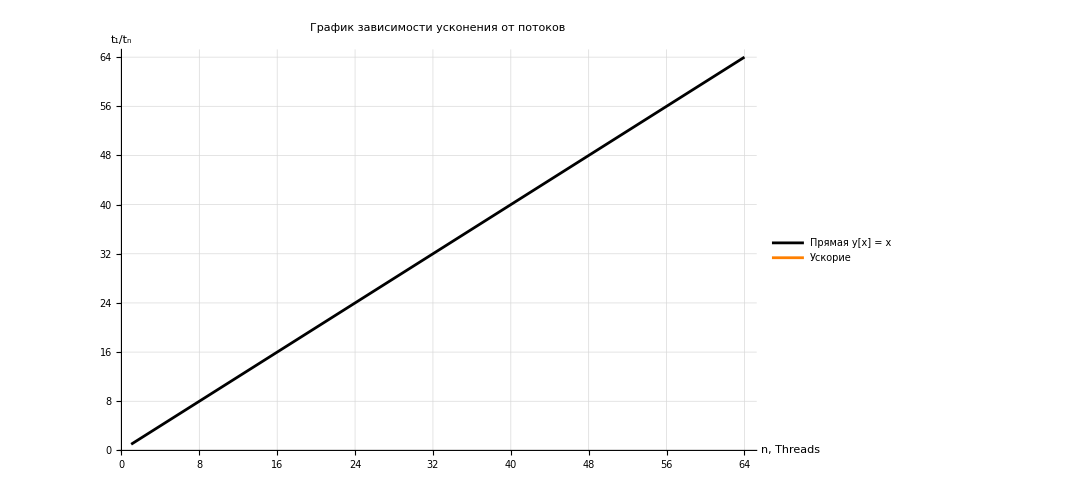

```mathematica
Show[
Plot[x, {x, 1, 64}, PlotStyle->Black, PlotLegends->{"Прямая y[x] = x"}],
ListLinePlot[Table[{data[[i]][[1]],(data[[2]][[2]])/(data[[i]][[2]])},{i,2,Length@data}],PlotStyle->Orange,PlotLegends->{"Ускорие"}],
GridLines->Automatic,AspectRatio->1/GoldenRatio,Axes->True,AxesStyle->{{Arrowheads[0.025],Black},{Arrowheads[0.03],Black}},
AxesLabel->{Style["n, Threads",Black,16,FontFamily->"Times"],Style["\!\(\*SubscriptBox[\(t\), \(1\)]\)/\!\(\*SubscriptBox[\(t\), \(n\)]\)",Black,16,FontFamily->"Times"]},LabelStyle->Directive[Black,14,FontFamily->"Times"],ImageSize->{800,500},PlotRange->All,PlotLabel->"График зависимости усконения от потоков"]
```